This Mathematica notebook supplements the paper : Patryk Mach, Adam Cieślik, Andrzej Odrzywołek, “Monte Carlo methods for stationary solutions of general-relativistic Vlasov systems: Collisionless accretion onto a moving Schwarzschild black hole’’, arXiv:2406.04471. It contains an example of a Monte Carlo simulation of a planar accretion model in the Schwarzschild spacetime . Asymptotically the gas obeys the Maxwell - Jüttner distribution .

Author : Adam Cieślik

## Notebook style

### General

In the section below, I have configured the visual style of the entire notebook with the following objectives:
	- Ensuring that cells containing code are delineated by borders, facilitating a clear visual distinction from textual content.
	- Adopting the “Latin Modern Roman” font for all textual elements.
	- Displaying an estimated execution time in seconds on the right side of each code cell.
Each setting is indicated in the subsequent code and can be adjusted as desired.

```mathematica
SetOptions[EvaluationNotebook[],
	StyleDefinitions->Notebook[
		{
		(* A general theme, of the entire notebook *)
		Cell[StyleData[StyleDefinitions->"Default.nb"]],
		(* Font settings for the text *)
		Cell[StyleData["Text"],FontFamily->"Latin Modern Roman",FontSlant->"Plain"],
		(* Font settings for titles *)
		Cell[StyleData["Title"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],Cell[StyleData["Subtitle"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],
		Cell[StyleData["Chapter"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],Cell[StyleData["Section"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],
		Cell[StyleData["Subsection"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],Cell[StyleData["Subsubsection"],FontFamily->"Latin Modern Roman",FontWeight->"Plain"],
		(* Cell borders *)
		Cell[
			StyleData["Input"],CellFrame->1,CellFrameColor->GrayLevel[0.5],
			(* Setting the displaying of the execution time  *)
			CellProlog:>(in=AbsoluteTime[]),
			CellEpilog:>(CurrentValue[EvaluationCell[],CellFrameLabels]={{None,Cell[BoxData[StyleBox[RowBox[{"(",ToBoxes[NumberForm[AbsoluteTime[]-in,{Infinity,1}]],")"}],Plain]]]},{None,None}})
			]
		},
		StyleDefinitions->"PrivateStylesheetFormatting.nb"
	]
	]
```

If you prefer the original style, execute the provided code, and the notebook will revert to its default appearance .

```mathematica
SetOptions[EvaluationNotebook[],DefaultStyleDefinitions->"Default.nb"]
```

### MaTeX

I also use the MaTex package here so that all plots are made in LaTex style

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
If[$OperatingSystem=="Windows",userProfile=FileNameJoin[{$HomeDirectory,"AppData","Local","Programs","MiKTeX","miktex","bin","x64","pdflatex.exe"}];
ConfigureMaTeX["pdfLaTeX"->userProfile,"Ghostscript"->"C:\\Program Files\\gs\\gs9.55.0\\bin\\gswin64c.exe"]
];
```

```mathematica
If[$OperatingSystem=="MacOSX",ConfigureMaTeX[
"pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"
]];
```

```mathematica
If[$OperatingSystem=="Unix",ConfigureMaTeX["pdfLaTeX"->"/usr/bin/pdflatex","Ghostscript"->"/usr/bin/gs"]];
```

```mathematica
ConfigureMaTeX[]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→/Library/TeX/texbin/pdflatex,Ghostscript→/usr/local/bin/gs}

```mathematica
SetOptions[MaTeX,FontSize->16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Setup of the basic quantities

```mathematica
ClearAll["Global`*"]
```

α and β form Maxwell - Jüttner distribution function:

```mathematica
α = 1;
β = 1;
```

Mass of the test particle and the black hole:

```mathematica
m=1;
M=1;
```

Mass of the test particle and the black hole:

```mathematica
xξ0=300;
```

The radius of the circle at which we are counting:

```mathematica
r0=8;
```

Velocity of the boost and the Lorentz factor:

```mathematica
v=0.95; 
γ=1/Sqrt[1-v^2];
```

The maximum energy of the particle to which we limit the simulation:

```mathematica
energycutoff=10;
```

A precision goal for Mathematica numerical integrals:

```mathematica
precision = 4;
```

## Analytical solutions

### Definitions of currents

In this Notebook, λ_c and λ_max are represented using two distinct approaches: one is applied here, and the other within the Monte Carlo simulation section. In the simulation segment, we can express both variables precisely as they appear in the literature. However, in this section, due to the requirements of numerical integration by Mathematica, their representations need slight modifications. Employing the same definitions for both numerical integrals and simulations could lead to numerical inaccuracies. To avoid confusion and ensure clarity in their application, I have added the suffix “Anal” to these variables when used in analytical contexts here. This differentiation is crucial for maintaining the integrity of the numerical calculations.

```mathematica
λcAnal[Infinity] = Infinity;
```

```mathematica
λcF =
	 Function[ϵ,
		Piecewise[
			{{12/(1 - 4/(1 + Sqrt[1 + 1/(-1 + (9 ϵ^2)/8)])^2) //Sqrt, ϵ < 10^4}}, 3 Sqrt[3 ϵ^2 - 1]
		]
	];
```

```mathematica
λcAnal[ϵ_?NumericQ] := λcF[ϵ];
```

```mathematica
λmaxAnal[ξ_?NumericQ, ϵ_?
      NumericQ] := ξ Sqrt[ϵ^2/(1 - 2/ξ) - 1]
```

Definition of the minimum permissible energy

```mathematica
ϵmin[ξ_] := 
	Piecewise[
		{{Infinity, ξ <= 3}, {Sqrt[(1 - 2/ξ) (1 + 1/(ξ - 3))], ξ <= 4}},1
	]
```

For our calculations, we require the elliptic integral defined as follows:
	X(ξ, ε, λ)= λ ∫_ξ^∞ 1/(ξ^2 √(ε^2-(1-2/ξ)(1+λ^2/ξ^2)))ⅆξ
In the Monte Carlo simulation section, elliptic functions are utilized to represent this integral, which is a standard approach for such calculations. However, to optimize the efficiency of numerical computations in this specific section, we employ an alternative strategy. We use the double exponent method for encoding the integral, implemented in C, and store the code in a directory named “EllipticX”. For the code provided below to function correctly, it is essential that the “EllipticX” folder is placed in the same directory as this Notebook. This encoding method and its implementation were developed by Andrzej Odrzywołek.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
lib=CreateLibrary[{"EllipticX.cpp"},"EllipticX"];
```

```mathematica
EllipticX=LibraryFunctionLoad[lib,"EllipticX",{Real,Real,Real},Real];
```

```mathematica
X[ξ_, ϵ_, 0] := 0
```

```mathematica
X[ξ_, Infinity, λ_] := 0
```

```mathematica
X[ξ_?NumericQ, ϵ_?NumericQ, λ_?NumericQ] := 
 EllipticX[ξ, ϵ, λ]
```

We will define currents J_μ. The letter D at the end denotes lower indices (covariant quantity) and U denotes upper indices (contravariant quantity).

```mathematica
JtInnerAbsFD = 
	Function[{ξ, ϕ, ϵ,v}, 
		(-2* α m^3/ξ)* NIntegrate[
			((ⅇ^(-β*γ*(ϵ+v*√(ϵ^2-1)*Cos[ϕ]*Cos[X[ξ,ϵ,λ]]))*Cosh[β γ v √(ϵ^2-1)Sin[ϕ]Sin[X[ξ,ϵ,λ]]]) ϵ)/(√(ϵ^2-(1-2/ξ)(1+λ^2/ξ^2))),
			{λ, 0, λcAnal[ϵ]}, Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JtInnerAbsD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JtInnerAbsFD[ξ, ϕ, ϵ,v];

JtAbsD = 
	Function[{ξ, ϕ,v}, 
		NIntegrate[  
			JtInnerAbsD[ξ, ϕ, ϵ,v], {ϵ, 1,energycutoff}, Method -> {"GlobalAdaptive"}, PrecisionGoal -> precision
		]
	];
```

```mathematica
JtInnerScattFD = 
	Function[{ξ, ϕ, ϵ,v},
		( -4α m^3/ξ)*NIntegrate[
			( ⅇ^(-β γ ϵ) ϵ Cosh[β γ v √(ϵ^2-1) Cos[ϕ] Cos[X[ξ,ϵ,λ]]] Cosh[β γ v √(ϵ^2-1) Sin[ϕ] Sin[X[ξ,ϵ,λ]]])/(√(ϵ^2-(1-2/ξ)(1+λ^2/ξ^2))),
			{λ, λcAnal[ϵ], λmaxAnal[ξ,ϵ]}, Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JtInnerScattD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JtInnerScattFD[ξ, ϕ, ϵ,v];

JtScattD =
	Function[{ξ, ϕ,v}, 
		If[ξ <= 3 (* No scattering below photon sphere *),
			 0,
			NIntegrate[
				JtInnerScattD[ξ, ϕ, ϵ,v], {ϵ, ϵmin[ξ], energycutoff}, Method -> {"GlobalAdaptive"}, PrecisionGoal -> precision
			]
		]
	];
```

```mathematica
JrInnerAbsFD = 
	Function[{ξ, ϕ, ϵ,v},
		(- 2α m^3/(ξ-2))*NIntegrate[
			(ⅇ^(-β*γ*(ϵ+v*√(ϵ^2-1)*Cos[ϕ]*Cos[X[ξ,ϵ,λ]]))*Cosh[β*γ*v*√(ϵ^2-1)*Sin[ϕ]*Sin[X[ξ,ϵ,λ]]]),
			{λ, 0, λcAnal[ϵ]}, Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JrInnerAbsD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JrInnerAbsFD[ξ, ϕ, ϵ,v];

JrAbsD = 
	Function[{ξ, ϕ,v}, 
		NIntegrate[
			JrInnerAbsD[ξ, ϕ, ϵ,v], {ϵ, 1, energycutoff}, Method -> {"GlobalAdaptive"}, PrecisionGoal -> precision
		]
	];
```

```mathematica
JrInnerScattFD = 
	Function[{ξ, ϕ, ϵ,v},  
		(4α m^3/(ξ-2))*NIntegrate[
			 ⅇ^(-β γ ϵ)Sinh[β γ v √(ϵ^2-1) Cos[ϕ] Cos[X[ξ,ϵ,λ]]] Cosh[β γ v √(ϵ^2-1) Sin[ϕ] Sin[X[ξ,ϵ,λ]]] ,
			{λ, λcAnal[ϵ], λmaxAnal[ξ,ϵ]}, Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JrInnerScattD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JrInnerScattFD[ξ, ϕ, ϵ,v];

JrScattD = 
	Function[{ξ, ϕ,v},
		If[ξ <= 3 (* No scattering below photon sphere *), 
			0,
				NIntegrate[
					JrInnerScattD[ξ, ϕ, ϵ,v], {ϵ,ϵmin[ξ],energycutoff}, Method -> {"GlobalAdaptive"},PrecisionGoal -> precision
			]
		]
	];
```

```mathematica
JφInnerAbsFD = 
	Function[{ξ, ϕ, ϵ,v}, 
		(-2α m^3*M/ξ)*NIntegrate[
				(ⅇ^(-β*γ*(ϵ+v*√(ϵ^2-1)*Cos[ϕ]*Cos[X[ξ,ϵ,λ]])) λ Sinh[β γ v √(ϵ^2-1)Sin[ϕ]Sin[X[ξ,ϵ,λ]]])/(√(ϵ^2-(1-2/ξ)(1+λ^2/ξ^2))),
			{λ, 0, λcAnal[ϵ]},Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JφInnerAbsD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JφInnerAbsFD[ξ, ϕ, ϵ,v];

JφAbsD = 
	Function[{ξ, ϕ,v}, 
		NIntegrate[  
			JφInnerAbsD[ξ, ϕ, ϵ,v], {ϵ, 1,energycutoff}, Method -> {"GlobalAdaptive"},PrecisionGoal -> precision
		]
	];
```

```mathematica
JφInnerScattFD = 
	Function[{ξ, ϕ, ϵ,v}, 
		(-4α m^3*M/ξ)*NIntegrate[
			( ⅇ^(-β γ ϵ) λ Sinh[β γ v √(ϵ^2-1) Sin[ϕ] Sin[X[ξ,ϵ,λ]]] Cosh[β γ v √(ϵ^2-1) Cos[ϕ] Cos[X[ξ,ϵ,λ]]] )/(√(ϵ^2-(1-2/ξ)(1+λ^2/ξ^2))),
			{λ, λcAnal[ϵ], λmaxAnal[ξ,ϵ]},Method -> {"LocalAdaptive", "SymbolicProcessing" -> False}
		]
	]; 

JφInnerScattD[ξ_?NumericQ, ϕ_?NumericQ, ϵ_?NumericQ,v_?NumericQ] := JφInnerScattFD[ξ, ϕ, ϵ,v];

JφScattD = 
	Function[{ξ, ϕ,v}, 
		If[ξ <= 3 (* No scattering below photon sphere *), 
			0,
			NIntegrate[
				JφInnerScattD[ξ, ϕ, ϵ,v], {ϵ, ϵmin[ξ],energycutoff}, Method -> {"GlobalAdaptive"},PrecisionGoal -> precision
			]
		]
	];
```

```mathematica
JtAbsU[ξ_,ϕ_,v_]:=(1/(1-2/ξ))*JtAbsD[ξ,ϕ,v];
```

```mathematica
JtScattU[ξ_,ϕ_,v_]:=(1/(1-2/ξ))*JtScattD[ξ,ϕ,v];
```

```mathematica
JrAbsU[ξ_,ϕ_,v_]:=(1-2/ξ)*JrAbsD[ξ,ϕ,v];
```

```mathematica
JrScattU[ξ_,ϕ_,v_]:=(1-2/ξ)*JrScattD[ξ,ϕ,v];
```

```mathematica
JφAbsU[ξ_,ϕ_,v_]:=1/ξ^2*JφAbsD[ξ,ϕ,v];
```

```mathematica
JφScattU[ξ_,ϕ_,v_]:=1/ξ^2*JφScattD[ξ,ϕ,v];
```

### Particle number density

As the initial and foremost validation step for the definitions programmed earlier, I will assess the behaviour of particle density. This evaluation involves utilizing the definition of covariant particle number density and normalizing it by its asymptotic value at infinity, which is a well-defined constant with additional details provided in the associated paper. A convergence of the ratio towards 1 with increasing distance would indicate a correct implementation of the J_μ quantities.

```mathematica
n[ξ_,ϕ_,v_]:=√((1/(1-2/ξ))*(JtAbsD[ξ,ϕ,v]+JtScattD[ξ,ϕ,v])^2-(1-2/ξ)*(JrAbsD[ξ,ϕ,v]+JrScattD[ξ,ϕ,v])^2-1/ξ^2*(JφAbsD[ξ,ϕ,v]+JφScattD[ξ,ϕ,v])^2)//Chop;
ninf=2*Pi*α*m^3*(1+β)/β^2*Exp[-β]//N;
```

Due to potential numerical difficulties encountered by Mathematica in rendering plots for the function n[φ] at the arguments 0, π/2 ​, and π, I have employed a strategy to circumvent these issues . To achieve this, I introduce a small quantity, “fi0”, set to 10^-6, which is then added to the aforementioned problematic argument values of the n[φ] function when plotting . This adjustment involves values very close to the original arguments but helps to avoid the numerical problems typically associated with plotting at these precise points.

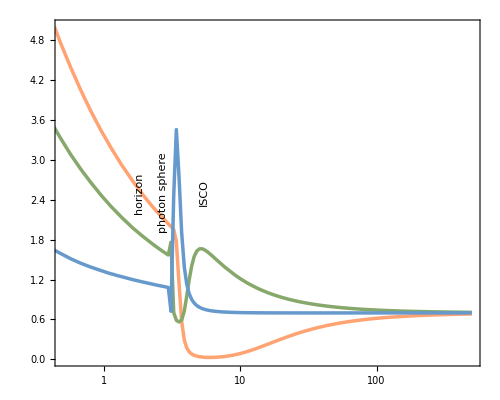

```mathematica
fi0=10^-6;
LogLinearPlot[{n[x,fi0,v]/ninf//Re,n[x,fi0+Pi/2,v]/ninf//Re,n[x,fi0+Pi,v]/(ninf//Re)},{x,0.1, 500},
	PlotRange->{{0.5,500},{0,5}},
	AspectRatio->0.8,
	PlotStyle->{
		Directive[Thickness[0.005],RGBColor[1.,0.64,0.45]],
		Directive[Thickness[0.005],RGBColor[0.53,0.66,0.42]],
		Directive[Thickness[0.005],RGBColor[0.4,0.6,0.8]]
	},
	ImageSize->500,
	GridLines->{{{2,Dashed},{3,Dashed},{6,Dashed}},{}},
	GridLinesStyle->{Directive[Gray]},
	Epilog->{
		Text[Rotate["horizon",90 Degree],{Log[2]-0.1,2.5}],
		Text[Rotate["photon sphere",90 Degree],{Log[3]-0.1,2.5}],
		Text[Rotate["ISCO",90 Degree],{Log[6]-0.1,2.5}]
	},
	Frame->True,
	FrameStyle->Black,
	(* Labelling with the help of the MaTex *) 
	FrameLabel->MaTeX/@{"\xi"," n/n_{\infty}"},
	LabelStyle->{FontFamily->"CMU Serif",FontSize->12},
	PlotLegends->Placed[MaTeX/@{"\varphi = 10^{-6}\approx 0","\varphi =  10^{-6} + \pi/2 \approx\pi/2","\varphi = 10^{-6} + \pi\approx\pi"},{0.8,0.7}],
	(* Functions to improve performance *)
	PerformanceGoal->"Speed",
	PlotPoints->50,
	MaxRecursion->2
]
```

```mathematica
NotebookSave[]
```

### Plots

The plots below are optimized using three key options to balance between performance and accuracy:
	- PerformanceGoal -> “Speed”: This option prioritizes the speed of graph generation, making it ideal for scenarios where quick rendering is more critical than capturing every minute detail of the plot.
	- PlotPoints: This parameter controls the initial number of sample points used in plotting. A higher number of PlotPoints increases the resolution and accuracy of the plot by considering more data points at the cost of slower graph generation. For a generally smooth function without rapid oscillations, a lower PlotPoints value, such as 50 or 100, may suffice.
	- MaxRecursion: This option dictates the depth of the recursive subdivision of the plotting interval. Suppose the plotted function is smooth and lacks sharp variations within the interval of interest. A lower MaxRecursion value (e.g., MaxRecursion -> 2 or MaxRecursion -> 1) can expedite the rendering process while sacrificing some detail. Conversely, for functions characterized by rapid changes, sharp peaks, or other complexities, a higher MaxRecursion level is recommended to achieve sufficient plot fidelity. Starting with MaxRecursion -> 3 or MaxRecursion -> 4 and adjusting upwards as needed can help capture the essential characteristics of the function.

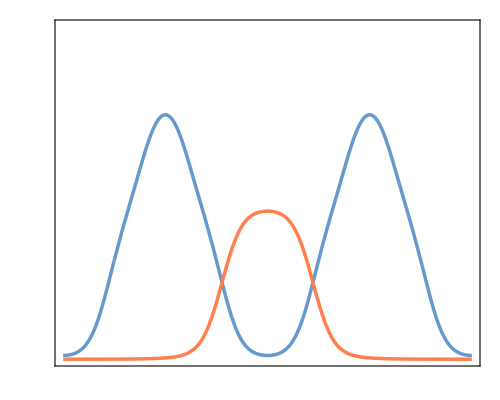

```mathematica
JtAnalytic2D=
	Plot[{-JtScattD[r0,φ,v],-JtAbsD[r0,φ,v]},{φ,0,2Pi},
		PlotRange->{{0,2Pi},{0,18}},
		AspectRatio->0.8,
		PlotStyle->{
			Directive[Thickness[0.005],RGBColor[0.4,0.6,0.8]],
			Directive[Thickness[0.005],RGBColor[1,0.5,0.31]]
		},
		ImageSize->500,
		Frame->True,
		FrameStyle->Black,
		(* Labelling with the help of the MaTex *) 
		FrameLabel->MaTeX/@{"\varphi"," J_t/(\alpha m_0^3)"},
		LabelStyle->{FontFamily->"CMU Serif",FontSize->12},
		FrameTicks->{
			(*Options for the Y axis*)
			{
				(* Marks on the left axis *)
				Join[
					(*More frequent lines every 1 without labels*)
					Table[{n ,""},{n,0,18}],
					(*Less frequent lines every 5 with labels*)
					With[{ticks=5 Range[0,20]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n,""},{n,0,18}]
			},
			(*Options for the X axis*)
			{
				(* Marks on the lower axis *)
				Join[
					(*More frequent lines every Pi/8 without labels*)
					Table[{n Pi/8,""},{n,0,16}],
					(*Less frequent lines every Pi/4 with labels*)
					With[{ticks=Pi/4 Range[0,8]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n Pi/8,""},{n,0,16}]
			}
		},
		PlotLegends->Placed[MaTeX/@{"-J_t^{\mathrm{(scat)}}/(\alpha m_0^3)","-J_t^{\mathrm{(abs)}}/(\alpha m_0^3)"},{0.8,0.85}],
		(* Functions to improve performance *)
		PerformanceGoal->"Speed",
		PlotPoints->50,
		MaxRecursion->2
	]
```

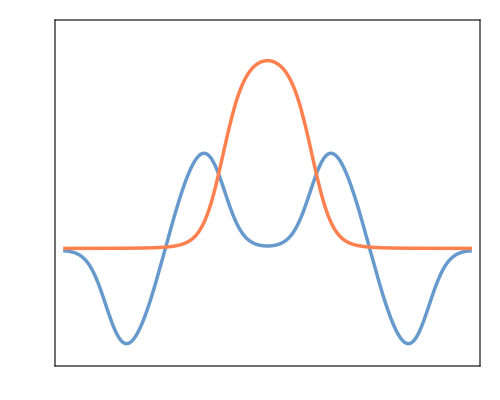

```mathematica
JrAnalytic2D=
	Plot[{-JrScattD[r0,φ,v],-JrAbsD[r0,φ,v]},{φ,0,2Pi},
		PlotRange->{{0,2Pi},{-6,12}},
		AspectRatio->0.8,
		PlotStyle->{
			Directive[Thickness[0.005],RGBColor[0.4,0.6,0.8]],
			Directive[Thickness[0.005],RGBColor[1,0.5,0.31]]
		},
		ImageSize->500,
		Frame->True,
		FrameStyle->Black,
		(* Labelling with the help of the MaTex *) 
		FrameLabel->MaTeX/@{"\varphi"," J_r/(\alpha m_0^3)"},
		LabelStyle->{FontFamily->"CMU Serif",FontSize->12},
		FrameTicks->{
			(*Options for the Y axis*)
			{
				(* Marks on the left axis *)
				Join[
					(*More frequent lines every 1 without labels*)
					Table[{n ,""},{n,-6,12}],
					(*Less frequent lines every 5 with labels*)
					With[{ticks=5 Range[-10,15]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n,""},{n,-6,12}]
			},
			(*Options for the X axis*)
			{
				(* Marks on the lower axis *)
				Join[
					(*More frequent lines every Pi/8 without labels*)
					Table[{n Pi/8,""},{n,0,16}],
					(*Less frequent lines every Pi/4 with labels*)
					With[{ticks=Pi/4 Range[0,8]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n Pi/8,""},{n,0,16}]
			}
		},
		PlotLegends->Placed[MaTeX/@{"-J_r^{\mathrm{(scat)}}/(\alpha m_0^3)","-J_r^{\mathrm{(abs)}}/(\alpha m_0^3)"},{0.8,0.85}],
		(* Functions to improve performance *)
		PerformanceGoal->"Speed",
		PlotPoints->50,
		MaxRecursion->2
	]
```

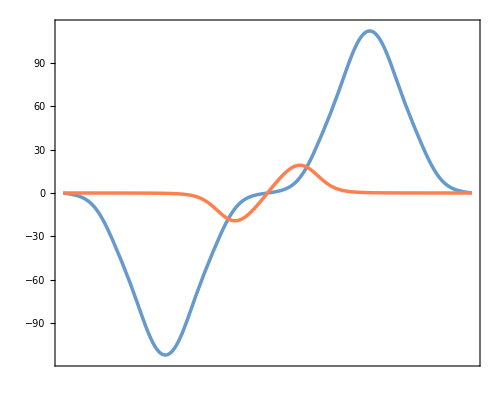

```mathematica
JφAnalytic2D=
	Plot[{JφScattD[r0,φ,v]//Re,JφAbsD[r0,φ,v]//Re},{φ,0,2Pi},
		PlotRange->{{0,2Pi},{-115,115}},AspectRatio->0.8,
		PlotStyle->{
			Directive[Thickness[0.005],RGBColor[0.4,0.6,0.8]],
			Directive[Thickness[0.005],RGBColor[1,0.5,0.31]]
		},
		ImageSize->500,
		Frame->True,
		FrameStyle->Black,
		(* Labelling with the help of the MaTex *) 
		FrameLabel->MaTeX/@{"\varphi"," J_\varphi/(\alpha m_0^3)"},
		LabelStyle->{FontFamily->"CMU Serif",FontSize->12},
		FrameTicks->{
			(*Options for the Y axis*)
			{
				(* Marks on the left axis *)
				Join[
					(*More frequent lines every 1 without labels*)
					Table[{n ,""},{n,-120,120,10}],
					(*Less frequent lines every 5 with labels*)
					With[{ticks=50 Range[-150,150]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n,""},{n,-120,120,10}]
			},
			(*Options for the X axis*)
			{
				(* Marks on the lower axis *)
				Join[
					(*More frequent lines every Pi/8 without labels*)
					Table[{n Pi/8,""},{n,0,16}],
					(*Less frequent lines every Pi/4 with labels*)
					With[{ticks=Pi/4 Range[0,8]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]]
				],
				(* Marks on the upper axis *)
				Table[{n Pi/8,""},{n,0,16}]
			}
		},
		PlotLegends->Placed[MaTeX/@{"J_\varphi^{\mathrm{(scat)}}/(\alpha m_0^3)","J_\varphi^{\mathrm{(abs)}}/(\alpha m_0^3)"},{0.8,0.2}],
		(* Functions to improve performance *)
		PerformanceGoal->"Speed",
		PlotPoints->50,
		MaxRecursion->2
	]
```

```mathematica
NotebookSave[]
```

## Monte Carlo simulation

### Basic definitions

This function calculates the angle that the particle will cover when moving from ξ_0 to ξ, regardless of the initial angle ψ_0. This angle is known as the true anomaly. The function implements integral (C.2):
	Y(ξ, ε, λ)= λ ∫_ξ_0^ξ 1/(ξ^2 √(ε^2-(1-2/ξ)(1+λ^2/ξ^2)))ⅆξ,
which is described in a paper by A. Cieślik and P. Mach titled “Revisiting Timelike and Null Geodesics in the Schwarzschild Spacetime: General Expressions in Terms of Weierstrass Elliptic Functions”, published in 2022.

```mathematica
Yscat[x_,{ϵr_,x0_,e_,λ_}]:=
	Module[{y,g2,g3,ys,y1,y2,y3,k2,X,X0},
		g2=1/12-1/λ^2;
		g3=1/6^3-1/(12 λ^2)-(e^2-1)/(4 λ^2);
		ys=Sort[N[y/.Solve[4 y^3 - g2 y -g3==0,y]]];
		y1=ys[[1]];
		y2=ys[[2]];
		y3=ys[[3]];
		k2=(y2-y1)/(y3-y1);
		-ϵr/Sqrt[y3-y1]*(EllipticF[ArcCos[Sqrt[(y2+1/12-1/(2x))/(y2-y1)]],k2]-EllipticF[ArcCos[Sqrt[(y2+1/12-1/(2x0))/(y2-y1)]],k2])
	]
```

```mathematica
Yabs[x_,{x0_,e_,λ_}]:=
	Module[{y,g2,g3,poly,yreal,part2,q,p,mu,k2,X},
		g2=1/12-1/λ^2;
		g3=1/6^3-1/(12 λ^2)-(e^2-1)/(4 λ^2);
		poly=4y^3-g2 y - g3;
		yreal=First[y/.Solve[poly==0,y,Reals,WorkingPrecision->10]];
		part2=FactorList[poly][[3,1]];
		q=SeriesCoefficient[part2,{y,0,0}];
		p=SeriesCoefficient[part2,{y,0,1}];
		mu=Sqrt[part2/.{y->yreal}];
		k2=(1/2)(1-(yreal+p/2)/mu);
		1/(2Sqrt[mu])*(EllipticF[2ArcTan[Sqrt[(-1/12+1/(2x)-yreal)/mu]],k2]-EllipticF[2ArcTan[Sqrt[(-1/12+1/(2x0)-yreal)/mu]],k2])
	]
```

The pericenter radius for an unbound scattered orbit.

```mathematica
ξperi[ϵ_,λ_]:=
	Module[{a0,a1,a2,a3,a4,f,ξ},
		a0=(ϵ^2-1)/λ^2;
		a1=1/(2 λ^2);
		a2=-1/6;
		a3=1/2;
		a4=0;
		f=a0 ξ^4 + 4 a1 ξ^3 + 6 a2 ξ^2 + 4 a3 ξ+a4;
		Max[ξ/.Solve[f==0,ξ]]
	]
```

Select “num” radom data.

```mathematica
num=10^6;
```

This is the place where you need to define the angular momentum differently

```mathematica
Clear[λc,λmax]
```

Critical angular momentum for a given energy ϵ.

```mathematica
λc[ϵ_]:=Sqrt[12/(1-4/(1+3ϵ/Sqrt[9 ϵ^2 - 8])^2)]
```

Maximal angular momentum for a geodesic of energy ϵ at the radius ξ.

```mathematica
λmax[ϵ_,ξ_]:=ξ Sqrt[ϵ^2 ξ/(ξ-2)-1]
```

```mathematica
λcutoff=λmax[energycutoff,xξ0];
```

### Random data generation

#### For ϵ_r = -1

```mathematica
normM=NIntegrate[Exp[-β/(√(1-v^2))*(ε+v*√(ε^2-1)*Cos[φ])],{φ,0,2*Pi},{ε,1,energycutoff}]
```

1.88968

```mathematica
distM=ProbabilityDistribution[Exp[-β/(√(1-v^2))*(ε+v*√(ε^2-1)*Cos[φ])]/normM,{ε,1,energycutoff},{φ,0,2*Pi}];
```

Plot of the 3D distribution

```mathematica
PDF[distM,{ε,φ}]
```

Piecewise[{{0.529192 ⅇ^(-3.20256 (ε+0.95 √(-1+ε^2) Cos[φ])), 1<ε<10&&0<φ<2 π}, {0, True}}]

```mathematica
Plot3D[PDF[distM,{ε,φ}],{ε,1,energycutoff},{φ,0,2*Pi},AxesLabel->{"ε","φ"}]
```

-Graphics3D-

In order to generate data from a given multidimensional distribution, I use the Markov Chain Monte Carlo (MCMC) method implemented with the RandomVariate function in Mathematica. When using RandomVariate with MCMC, several parameters can be adjusted to control how samples are generated. Two important parameters are “Thinning” and “InitialVariance”.
	- “Thinning” is a technique used in MCMC to reduce the correlation between consecutive samples in the chain. When you set the value of “Thinning” to 1, every sample is retained, and no thinning occurs. However, if you set a higher value, say 10, only the tenth sample from the chain is retained, and the rest are discarded. This helps obtain more independent samples, but it also increases the time required to generate a large number of samples.
	- The “InitialVariance” parameter determines the initial variance of the sample distribution in the MCMC algorithm. This variance affects how far apart subsequent samples in the chain can be placed. Generally, a value of 1 is considered a standard setting that works well in most cases. However, if your data has a different scale or the MCMC algorithm faces difficulty achieving convergence, it might be worth tweaking this value.

```mathematica
dataM0=.
dataM0=RandomVariate[distM,num,Method->{"MCMC","Thinning"->2,"InitialVariance"->1}];
dataM=Transpose[{dataM0[[All,1]],RandomReal[{0,λcutoff},num],dataM0[[All,2]],RandomChoice[{-1,1},num]}];
```

Checking whether the randomly selected data fits the distribution by drawing a histogram.

Notes on commands for generating histograms
Method 1:
You can use the command 
Histogram[Table[dataM[[i]][[1]], {i, 1, Length[dataM]}], 50],
but it is slow.

Method 2 (more efficient):
Mathematica is optimized for vector operations, so it is better to operate directly on lists.

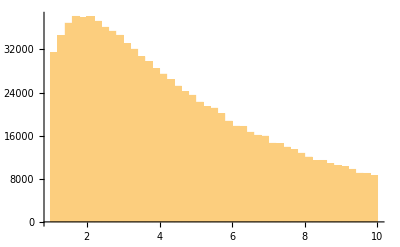

```mathematica
Histogram[dataM[[All,1]],50]
```

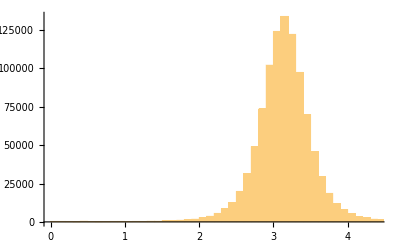

```mathematica
Histogram[dataM[[All,3]],50]
```

Dividing data into scattered and absorbed parts

```mathematica
Clear[results,ϵ,λ,φ0,dir]
results=
Table[{ϵ,λ,φ0,dir}=dataM[[i]][[1;;4]];
	λup=λmax[ϵ,xξ0];
	If[λ<λmax[ϵ,xξ0],
		{ϵ,λ,φ0,dir},Nothing
	],{i,1,num}
];
(* Filtering the results *)
scatM=Select[results,#[[2]]>λc[#[[1]]]&];
absM=Select[results,#[[2]]<=λc[#[[1]]]&];
```

```mathematica
Length[absM]
```

7408

```mathematica
Length[scatM]
```

414444

#### For ϵ_r = +1

```mathematica
normP=NIntegrate[Exp[-β/(√(1-v^2))*(ε-v*√(ε^2-1)*Cos[φ])],{φ,0,2*Pi},{ε,1,energycutoff}]
```

1.88968

```mathematica
distP=ProbabilityDistribution[Exp[-β/(√(1-v^2))*(ε-v*√(ε^2-1)*Cos[φ])]/normP,{ε,1,energycutoff},{φ,0,2*Pi}];
```

Plot of the 3D distribution

```mathematica
PDF[distP,{ε,φ}]
```

Piecewise[{{0.529192 ⅇ^(-3.20256 (ε-0.95 √(-1+ε^2) Cos[φ])), 1<ε<10&&0<φ<2 π}, {0, True}}]

```mathematica
Plot3D[PDF[distP,{ε,φ}],{ε,1,energycutoff},{φ,0,2*Pi},AxesLabel->{"ε","φ"}]
```

-Graphics3D-

```mathematica
dataP0=.

dataP0=RandomVariate[distP,num,Method->{"MCMC","Thinning"->2,"InitialVariance"->1}];
dataP=Transpose[{dataP0[[All,1]],RandomReal[{0,λcutoff},num],dataP0[[All,2]],RandomChoice[{-1,1},num]}];
```

Checking whether the randomly selected data fits the distribution by drawing a histogram.

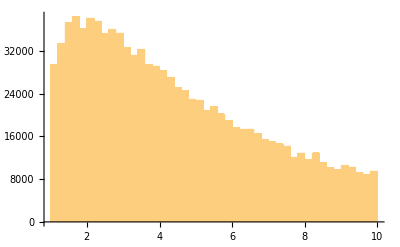

```mathematica
Histogram[dataP[[All,1]],50]
```

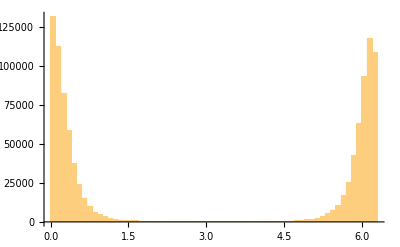

```mathematica
Histogram[dataP[[All,3]],50]
```

Dividing data into scattered and absorbed parts

```mathematica
Clear[results,ϵ,λ,φ0,dir]
results=
Table[{ϵ,λ,φ0,dir}=dataP[[i]][[1;;4]];
	λup=λmax[ϵ,xξ0];
	If[λ<λmax[ϵ,xξ0],
		{ϵ,λ,φ0,dir},Nothing
	],{i,1,num}
	];
(* Filtering the results *)
scatP=Select[results,#[[2]]>λc[#[[1]]]&];
absP=Select[results,#[[2]]<=λc[#[[1]]]&];
```

```mathematica
Length[absP]
```

7476

```mathematica
Length[scatP]
```

415926

### Volume setup

```mathematica
voltotM=NIntegrate[Exp[-β/(√(1-v^2))*(ε+v*√(ε^2-1)*Cos[φ])]λc[ε],{φ,0,2*Pi},{ε,1,energycutoff}]
```

42.4225

```mathematica
voltotM2=NIntegrate[Exp[-β/(√(1-v^2))*(ε+v*√(ε^2-1)*Cos[φ])](λmax[ε,xξ0]-λc[ε]),{φ,0,2*Pi},{ε,1,energycutoff}]
```

2348.11

```mathematica
voltotP=NIntegrate[Exp[-β/(√(1-v^2))*(ε-v*√(ε^2-1)*Cos[φ])]λc[ε],{φ,0,2*Pi},{ε,1,energycutoff}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

42.4225

```mathematica
voltotP2=NIntegrate[Exp[-β/(√(1-v^2))*(ε-v*√(ε^2-1)*Cos[φ])](λmax[ε,xξ0]-λc[ε]),{φ,0,2*Pi},{ε,1,energycutoff}]
```

2348.11

To assess the suitability of our data simulation method, we can compare the distribution of the simulated data with the expected distribution. We can achieve this by comparing the ratios of volumes in phase space occupied by different types of trajectories. If the ratios of these volumes match those observed in a set of randomly generated trajectories, it suggests the simulation method is capturing the desired behaviour.

```mathematica
N[Length[absM]/Length[scatM]]
```

0.0178745

```mathematica
voltotM/voltotM2
```

0.0180667

```mathematica
N[Length[absP]/Length[scatP]]
```

0.0179744

```mathematica
voltotP/voltotP2
```

0.0180667

### Counting trajectories of scattered trajectories in a circle with constant radius r_0

We choose the number of cells around the black hole in which we will count, that is, the number of pixels at a given distance r_0

```mathematica
nφ=360;
```

In the following code, I have implemented parallel processing to enhance computational speed . This allows the code to execute across multiple processors simultaneously . Below, you can specify the number of processors you want to use for these calculations . If you want to use all available processing options, replace the number 4 with the expression $ProcessorCount.

```mathematica
nSubsets= 4;
```

We designate the data file for reference, in this instance, ‘scatM’. To adapt this loop for ‘scatP’ trajectories, one should modify the data type accordingly; the remainder of the code will not require changes.

```mathematica
data=scatM;
```

We set the pixel width and normalization of the data.

```mathematica
dφ=2Pi/nφ;
normaliz=Length[data]dφ;
```

Dividing the' data' into subsets ensures comprehensive inclusion of all data points . By employing the UpTo option within the Partition function, the method accounts for all elements in the subsets, accommodating scenarios where the final subset contains fewer elements than the others.

```mathematica
dataSubsets=Partition[data,UpTo[Ceiling[Length[data]/nSubsets]]];
```

Function for parallel processing of a single subset of data

```mathematica
processSubset[subset_]:=
	Module[{countsLocal=Table[0,{pixel,1,nφ}],countsrLocal=Table[0,{pixel,1,nφ}],countsphiLocal=Table[0,{pixel,1,nφ}]},
		For[i=1,i<=Length[subset],i++,
			dir= subset[[i,4]];
			λ=subset[[i,2]];
			φ0=subset[[i,3]];
			ϵ=subset[[i,1]];
			per=ξperi[ϵ,λ]//Re;
			(* We check whether the particle is in front of the pericenter.If so,we perform calculations.If not,we skip it. *)
			If[r0>per,
				(* We calculate the angle at which the particle meets the target *)
				psiIN=φ0+dir*Yscat[r0,{-1,xξ0,ϵ,λ}]//Re;
				psiIN2=Mod[psiIN,2Pi];
				(* We convert the angle into a pixel *)
				pixelin=IntegerPart[psiIN2/dφ]+1;
				(* We calculate the values of the current coordinates *)
				weight=ϵ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
				weightr=1/(r0*(1-2/r0)); 
				weightphi=dir *λ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
				weight=2 weight* voltotM2/normaliz;
				weightrIN=2  weightr*voltotM2/normaliz;
				weightphi=2 weightphi*voltotM2/normaliz;
				countsLocal[[pixelin]]+=N[weight];
				countsrLocal[[pixelin]]+=N[weightrIN];
				countsphiLocal[[pixelin]]+=N[weightphi]
			];
		];
	(* Returning results as a list of lists *)
	{countsLocal,countsrLocal,countsphiLocal}
	];
```

Parallel processing of each subset

```mathematica
allResults=ParallelMap[processSubset,dataSubsets];
```

Combining results

```mathematica
finalCountsScatM=N[Total[allResults[[All,1]]]];
finalCountsrScatM=N[Total[allResults[[All,2]]]];
finalCountsphiScatM=N[Total[allResults[[All,3]]]];
```

We repeat the loop only for outgoing particles. Thus, apart from the initial values, we change the signs in weightrIN and weightphi. Moreover, we calculate psiIN differently.

```mathematica
nSubsets=4;
data=scatP;
dφ=2Pi/nφ;
normaliz=Length[data]dφ; 

dataSubsets=Partition[data,UpTo[Ceiling[Length[data]/nSubsets]]];

processSubset[subset_]:=
	Module[{countsLocal=Table[0,{pixel,1,nφ}],countsrLocal=Table[0,{pixel,1,nφ}],countsphiLocal=Table[0,{pixel,1,nφ}]},
		For[i=1,i<=Length[subset],i++,
			dir= subset[[i,4]];
			λ=subset[[i,2]];
			φ0=subset[[i,3]];
			ϵ=subset[[i,1]];
			per=ξperi[ϵ,λ]//Re;
			If[r0>per,
				psiIN=φ0+dir*Yscat[r0,{-1,xξ0,ϵ,λ}]//Re; (* here we change the counting direction Yscat[] *)
				psiIN2=Mod[psiIN,2Pi];
				pixelin=IntegerPart[psiIN2/dφ]+1;
				weight=ϵ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
				weightr=1/(r0*(1-2/r0)); 
				weightphi=dir *λ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
				weight=2 weight* voltotM2/normaliz;
				weightrIN=-2  weightr*voltotP2/normaliz; (* here we change the signs *)
				weightphi=-2 weightphi*voltotP2/normaliz;
				countsLocal[[pixelin]]+=N[weight];
				countsrLocal[[pixelin]]+=N[weightrIN];
				countsphiLocal[[pixelin]]+=N[weightphi]
			];
		];
	{countsLocal,countsrLocal,countsphiLocal} 
	];

allResults=ParallelMap[processSubset,dataSubsets];

finalCountsScatP=N[Total[allResults[[All,1]]]];
finalCountsrScatP=N[Total[allResults[[All,2]]]];
finalCountsphiScatP=N[Total[allResults[[All,3]]]];
```

The final results for scattered particles are obtained by adding the above two results in each pixel.

```mathematica
JtScattResults={};
JrScattResults={};
JphiScattResults={};
For[pixel=1,pixel<=nφ,pixel++,
	φdn=(pixel-1)dφ;
	φup=pixel dφ;
	φsr=(φdn+φup)/2;
	AppendTo[JtScattResults,{N[φsr] ,finalCountsScatM[[pixel]]+finalCountsScatP[[pixel]]}];
	AppendTo[JrScattResults,{N[φsr] ,finalCountsrScatM[[pixel]]+finalCountsrScatP[[pixel]]}];
	AppendTo[JphiScattResults,{N[φsr] ,finalCountsphiScatM[[pixel]]+finalCountsphiScatP[[pixel]]}];
	]
```

### Counting trajectories of absorbed trajectorie in a circle with constant radius r_0

We repeat the loop for absorbed particles using the corresponding data. We use the same code as for scattered entering particles.

```mathematica
nSubsets= 4; 
data=absM;
dφ=2Pi/nφ;
normaliz=Length[data]dφ; 

dataSubsets=Partition[data,UpTo[Ceiling[Length[data]/nSubsets]]];

processSubset[subset_]:=
	Module[{countsLocal=Table[0,{pixel,1,nφ}],countsrLocal=Table[0,{pixel,1,nφ}],countsphiLocal=Table[0,{pixel,1,nφ}]},
		For[i=1,i<=Length[subset],i++,
			dir= subset[[i,4]];
			λ=subset[[i,2]];
			φ0=subset[[i,3]];
			ϵ=subset[[i,1]];
			psiIN=φ0+dir*Yabs[r0,{xξ0,ϵ,λ}]//Re;
			psiIN2=Mod[psiIN,2Pi];
			pixelin=IntegerPart[psiIN2/dφ]+1;
			weight=ϵ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
			weightr=1/(r0*(1-2/r0)); 
			weightphi=dir *λ/(r0*Sqrt[ϵ^2-(1-2/r0)(1+λ^2/r0^2)]);
			weight=2 weight* voltotM/normaliz;
			weightrIN=2  weightr*voltotM/normaliz;
			weightphi=2 weightphi*voltotM/normaliz;
			countsLocal[[pixelin]]+=N[weight];
				countsrLocal[[pixelin]]+=N[weightrIN];
				countsphiLocal[[pixelin]]+=N[weightphi]
		];
	{countsLocal,countsrLocal,countsphiLocal} 
	];


allResults=ParallelMap[processSubset,dataSubsets];

(*Łączenie wyników*)
finalCountsAbs=N[Total[allResults[[All,1]]]];
finalCountsrAbs=N[Total[allResults[[All,2]]]];
finalCountsphiAbs=N[Total[allResults[[All,3]]]];
```

```mathematica
JtAbsResults={};
JrAbsResults={};
JphiAbsResults={};
For[pixel=1,pixel<=nφ,pixel++,
	φdn=(pixel-1)dφ;
	φup=pixel dφ;
	φsr=(φdn+φup)/2;
	AppendTo[JtAbsResults,{N[φsr] ,finalCountsAbs[[pixel]]}];
	AppendTo[JrAbsResults,{N[φsr] ,finalCountsrAbs[[pixel]]}];
	AppendTo[JphiAbsResults,{N[φsr] ,finalCountsphiAbs[[pixel]]}];
	]
```

### Plots

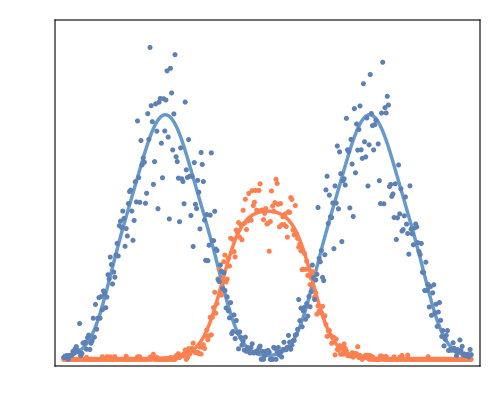

```mathematica
Show[JtAnalytic2D,ListPlot[JtAbsResults,PlotStyle->RGBColor[1,0.5,0.31]],ListPlot[JtScattResults]]
```

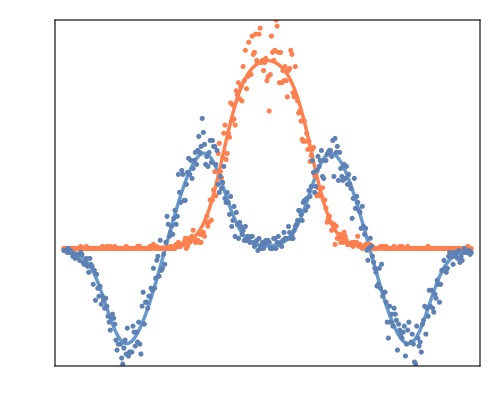

```mathematica
Show[JrAnalytic2D,ListPlot[JrAbsResults,PlotStyle->RGBColor[1,0.5,0.31]],ListPlot[JrScattResults]]
```

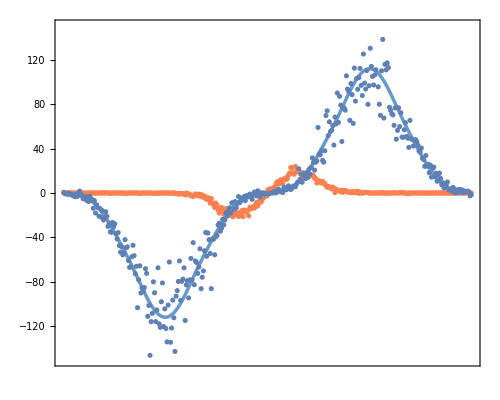

```mathematica
Show[JφAnalytic2D,ListPlot[JphiAbsResults,PlotStyle->RGBColor[1,0.5,0.31]],ListPlot[JphiScattResults],PlotRange->{{0,2Pi},{-150,150}}]
```

```mathematica
NotebookSave[]
```